```mathematica
Quit
```

## Dlogbasis

```mathematica
SetDirectory[NotebookDirectory[]<>"../../"]
```

/Users/corradini/fire/FIRE6

```mathematica
<<DlogBasis`
```

DlogBasis: Package for automated calculation of leading singularities and dlog integrands.
Pascal Wasser, Johannes Gutenberg University Mainz (2020).

```mathematica
Internal= {k1, k2,k3};
External= {p1,p2,p3};
Propagators={-k1^2,-(k1+p1)^2,-(k1+p1+p2)^2,-k2^2,-(k2-k1)^2,-(k3+k2-k1)^2,-(k2+k3+p1+p2)^2,-(k2+k3+p1+p2+p3)^2,-k3^2,-(k2+p1+p2+p3)^2,-(k2+p1)^2,-(k3+p1)^2,-(k1+p1+p2+p3)^2,-(k3+k1)^2,-(k2+p1+p2)^2};
Replacements= {p1^2->0,p2^2->0,p3^2->0,p1 p2->s/2,p1 p3->(-s-t)/2,p2 p3->t/2};
InitializeDlogbasis[];
```

```mathematica
SetParametrization[SpinorHelicityParametrization[Internal,{a,b,c},External]]
```

```mathematica
ansatz=IntegrandAnsatz[G[1,{1,1,1,1,1,1,1,1,1,1,0,0,0,0,0}]];
```

```mathematica
ansatz//Length
```

377

```mathematica
integrand=Parametrize[ansatz,n];
```

```mathematica
leadingsingularities=LeadingSingularities[integrand,IntegrandVariables[],n];
```

```mathematica
dlogs=GenerateDlogbasis[ansatz,leadingsingularities,n];
```

```mathematica
Export["FF/3LTC/dlog.m",(Cases[dlogs,_G,{0,Infinity}]/.{G[1,{a__}]:>{1,{a}}})//DeleteDuplicates]
Export["FF/3LTC/dlogBasis.m",dlogs]
```

FF/3LTC/dlog.m

FF/3LTC/dlogBasis.m

```mathematica
Quit[]
```

## Reduction using FIRE

```mathematica
SetDirectory[NotebookDirectory[]<>"../../"];
Get["FIRE6.m"];
```

FIRE, version 6.5.2

```mathematica
Internal= {k1, k2,k3};
External= {p1,p2,p3};
Propagators={-k1^2,-(k1+p1)^2,-(k1+p1+p2)^2,-k2^2,-(k2-k1)^2,-(k3+k2-k1)^2,-(k2+k3+p1+p2)^2,-(k2+k3+p1+p2+p3)^2,-k3^2,-(k2+p1+p2+p3)^2,-(k2+p1)^2,-(k3+p1)^2,-(k1+p1+p2+p3)^2,-(k3+k1)^2,-(k2+p1+p2)^2};
Replacements= {p1^2->0,p2^2->0,p3^2->0,p1 p2->s/2,p1 p3->(-s-t)/2,p2 p3->t/2};
```

```mathematica
PrepareIBP[];
Prepare[AutoDetectRestrictions->True,LI->True];
SaveStart["FF/3LTC/3LTC"];
Quit[];
```

Prepared

Dimension set to 15

No symmetries

Saving initial data

```mathematica
SetDirectory[NotebookDirectory[]<>"../../"];
SetDirectory["extra/LiteRed/Setup/"];
Get["LiteRed.m"];
SetDirectory["../../.."];
Get["FIRE6.m"];
Internal= {k1, k2,k3};
External= {p1,p2,p3};
Propagators={-k1^2,-(k1+p1)^2,-(k1+p1+p2)^2,-k2^2,-(k2-k1)^2,-(k3+k2-k1)^2,-(k2+k3+p1+p2)^2,-(k2+k3+p1+p2+p3)^2,-k3^2,-(k2+p1+p2+p3)^2,-(k2+p1)^2,-(k3+p1)^2,-(k1+p1+p2+p3)^2,-(k3+k1)^2,-(k2+p1+p2)^2};
Replacements= {p1^2->0,p2^2->0,p3^2->0,p1 p2->s/2,p1 p3->(-s-t)/2,p2 p3->t/2};
CreateNewBasis[b1,Directory->"./b3LTC.dir"];
GenerateIBP[b1];
AnalyzeSectors[b1,{__,0,0,0,0,0}];
FindSymmetries[b1,EMs->True];
DiskSave[b1];
Quit[];
```

**************** LiteRed v1.83 ********************
Author: Roman N. Lee, Budker Institute of Nuclear Physics, Novosibirsk.
Release Date: 11.01.2020
LiteRed stands for Loop InTEgrals REDuction.
The package is designed for the search and application of the Integration-By-Part reduction rules. It also contains some other useful tools.
Input file timestamp: Sun 7 Sep 2025 15:59:28
See ?LiteRed`* for a list of functions.

FIRE, version 6.5.2

Declare: {{k1,k2,k3,p1,p2,p3},Vector,{s,t},Number}

Lee propagators: {-(k1·k1),-((k1+p1)·(k1+p1)),-((k1+p1+p2)·(k1+p1+p2)),-(k2·k2),-((-k1+k2)·(-k1+k2)),-((-k1+k2+k3)·(-k1+k2+k3)),-((k2+k3+p1+p2)·(k2+k3+p1+p2)),-((k2+k3+p1+p2+p3)·(k2+k3+p1+p2+p3)),-(k3·k3),-((k2+p1+p2+p3)·(k2+p1+p2+p3)),-((k2+p1)·(k2+p1)),-((k3+p1)·(k3+p1)),-((k1+p1+p2+p3)·(k1+p1+p2+p3)),-((k1+k3)·(k1+k3)),-((k2+p1+p2)·(k2+p1+p2))}

Valid basis.
    Ds[b1] — denominators,
    SPs[b1] — scalar products involving loop momenta,
    LMs[b1] — loop momenta,
    EMs[b1] — external momenta,
    Toj[b1] — rules to transform scalar products to denominators.
The definitions of the basis will be saved in ./b3LTC.dir

DiskSave::overwrite: The file ./b3LTC.dir/b1 has been overwritten.

Integration-By-Part&Lorentz-Invariance identities are generated.
    IBP[b1] — integration-by-part identities,
    LI[b1] — Lorentz invariance identities.

Found 720 zero sectors out of 1024.
    ZeroSectors[b1] — zero sectors,
    NonZeroSectors[b1] — nonzero sectors,
    SimpleSectors[b1] — simple sectors (no nonzero subsectors),
    BasisSectors[b1] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[b1] — a rule to nullify all zero j[b1…],
    CutDs[b1] — a flag list of cut denominatorsj (1=cut).

Found 172 mapped sectors and 132 unique sectors.
    UniqueSectors[b1] — unique sectors.
    MappedSectors[b1] — mapped sectors.
    SR[b1][…] — symmetry relations for j[b1,…] from UniqueSectors[b1].
    jSymmetries[b1,…] — symmetry rules for the sector js[b1,…] in UniqueSectors[b1].
    jRules[b1,…] — reduction rules for j[b1,…] from MappedSectors[b1].

DiskSave::overwrite: The file BasisSectors[b1] has been overwritten.

DiskSave::overwrite: The file IBP[b1] has been overwritten.

DiskSave::overwrite: The file jRules[b1, 0, 0, 0, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0, 0, 0] has been overwritten.

General::stop: Further output of DiskSave::overwrite will be suppressed during this calculation.

```mathematica
SetDirectory[NotebookDirectory[]<>"../../"];
Get["FIRE6.m"];
LoadStart["FF/3LTC/3LTC"];
TransformRules["./b3LTC.dir","FF/3LTC/3LTC.lbases",1];
SaveSBases["FF/3LTC/3LTC"];
Quit[];
```

```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../../"];
Get["FIRE6.m"];
LoadStart["FF/3LTC/3LTC",1];
Burn[];
LoadTables["FF/3LTC/3LTC.tables"];
```

FIRE, version 6.5.2

Initial data loaded

```mathematica
InvCh=(Import["FF/3LTC/dlogBasis.m"]/.{G->F});
```

```mathematica
InvCh//Length
```

168

```mathematica
Export["FF/3LTC/mastersLad.m",F[1,{1,1,1,1,1,1,1,1,1,1,0,0,0,0,0}]];
Export["FF/3LTC/mastersLadCan.m",MasterIntegrals[]];
Export["FF/3LTC/invCh.m",InvCh];
```

## Change of basis from the canonical basis to the ‘Laporta’ one

```mathematica
Quit
```

```mathematica
<<FiniteFlow`
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../../"];
```

```mathematica
Can=Import["FF/3LTC/dlogBasis.m"];
InvCh=Import["FF/3LTC/invCh.m"];
masters=Import["FF/3LTC/mastersLadCan.m"]/.{{1,{a__}}->G[1,{a}]};
```

```mathematica
cs=Table[c[i],{i,1,Length[InvCh]}];
```

```mathematica
eqs=Table[
Coefficient[cs[[i]]InvCh[[i]],
masters],{i,Length[InvCh]}];
```

```mathematica
mysys = (Thread[Total[eqs]==0]//Collect[#,_c,Together]&)/.{d->4-2eps};
```

```mathematica
mysol = FFDenseSolve[mysys,cs];
```

```mathematica
mysol//Length
```

41

```mathematica
todel=(Cases[cs/.mysol,_c,Infinity]//DeleteDuplicates)/.c->List;
```

```mathematica
todel//Length
```

127

```mathematica
newCh=Delete[InvCh,todel];
newCan=Delete[Can,todel];
```

```mathematica
newCan//Length
```

41

```mathematica
Ms=Array[M,Length[masters]];
Gs=Array[G,Length[newCh]];
```

```mathematica
ChMat=Table[
Coefficient[newCh[[i]],
masters[[k]]],{i,Length[newCh]},{k,Length[masters]}];
```

```mathematica
BasisChange=FFInverse[ChMat/.{d->4-2eps}//Together,Parameters->{s,t,eps}];
```

```mathematica
Export["FF/3LTC/can.m",newCan];
Export["FF/3LTC/BasisCh.m",newCh];
Export["FF/3LTC/MIstoCan.m",BasisChange];
```

```mathematica
"FF/3LTC/can.m"
```

```mathematica
"FF/3LTC/MIstoCan.m"
```

```mathematica
"FF/3LTC/BasisCh.m"
```

```mathematica
Quit
```

```mathematica
"FF/3LTC/BoxinCan.m"
```

## Draw MIs

```mathematica
SetDirectory[NotebookDirectory[]<>"../../"];
```

```mathematica
<<LiteRed2`
```

**************** LiteRed v2.025β ********************
Author: Roman N. Lee, Budker Institute of Nuclear Physics, Novosibirsk.
Release Date: ????-??-??
Timestamp: Thu 20 Nov 2025 13:50:10
Read from:/Users/corradini/LiteRed2/Source/LiteRed2025.m (CRC32:749265139,{2340977437, 3317197336, 1063727846})

LiteRed stands for Loop integrals Reduction.
The package is designed for the search and application of the Integration-By-Part reduction rules. It also contains some other useful tools.

See ?LiteRed`* for a list of functions.

```mathematica
Declare[{k1,k2,k3,p1,p2,p3},Vector,{s,t},Number];
```

```mathematica
sp[p1,p1]=0;sp[p2,p2]=0;sp[p3,p3]=0;sp[p1,p2]=s/2;sp[p2,p3]=t/2;sp[p1,p3]=(-s-t)/2;
```

```mathematica
NewDsBasis[box3,{-(k1·k1),-((k1+p1)·(k1+p1)),-((k1+p1+p2)·(k1+p1+p2)),-(k2·k2),-((-k1+k2)·(-k1+k2)),-((-k1+k2+k3)·(-k1+k2+k3)),-((k2+k3+p1+p2)·(k2+k3+p1+p2)),-((k2+k3+p1+p2+p3)·(k2+k3+p1+p2+p3)),-(k3·k3),-((k2+p1+p2+p3)·(k2+p1+p2+p3)),-((k2+p1)·(k2+p1)),-((k3+p1)·(k3+p1)),-((k1+p1+p2+p3)·(k1+p1+p2+p3)),-((k1+k3)·(k1+k3)),-((k2+p1+p2)·(k2+p1+p2))},{k1,k2,k3},Directory->"box3dir"];
```

box3 is valid basis. The definitions of the basis will be saved in "box3dir" directory.
    Ds[box3] — denominators,
    SPs[box3] — scalar products involving loop momenta,
    LMs[box3] — loop momenta,
    EMs[box3] — external momenta,
    Parameters[box3] — parameters (invariants, masses, dimension),
    Toj[box3] — rules to transform scalar products to denominators,
    CutDs[box3] — flag vector of cut denominators.

```mathematica
topo={{8->1,0},{1->2,0},{2->3,0},{6->8,0},{8->7,0},{7->3,0},{3->5,0},{5->4,0},{4->7,0},{4->6,0},{-1->1,p1,0},{-2->2,p2,0},{-5->5,p3,0},{-6->6,p4,0}};
```

```mathematica
SetOptions[FeynGraphPlot,EdgeLabels->True,Frame->False]
```

{GraphLayout→SpringElectricalEmbedding,VertexCoordinates→Automatic,EdgeLabels→True,EdgeStyle→{_→{GrayLevel[0]}},VertexStyle→{_→{GrayLevel[0],Disk[{0,0}]}},VertexSize→{_→0.003},VertexLabels→None,VertexLabelStyle→{RGBColor[1, 0, 0]},Background→None,Frame→False,FrameLabel→None,FrameStyle→{},LabelStyle→{},ImageMargins→0,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→RGBColor[1, 0, 0],MultiedgeStyle→Automatic,PackingMethod→Automatic,PlotLabel→None,Epilog→{}}

```mathematica
AttachGraph[js[box3,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0],topo]
```

```mathematica
masters=Import["FF/3LTC/mastersLadCan.m"]/.{_,{a__}}:>j[box3,a]
```

{j[box3,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0],j[box3,0,0,1,1,1,0,0,1,1,0,0,0,0,0,0],j[box3,0,0,1,1,1,0,1,0,1,0,0,0,0,0,0],j[box3,0,0,1,1,1,1,0,1,1,0,0,0,0,0,0],j[box3,0,1,0,0,0,1,0,0,1,1,0,0,0,0,0],j[box3,0,1,0,0,1,0,1,0,1,1,0,0,0,0,0],j[box3,0,1,0,0,1,1,0,1,0,1,0,0,0,0,0],j[box3,0,1,0,0,1,1,1,0,1,1,0,0,0,0,0],j[box3,0,1,0,1,0,1,1,0,1,1,0,0,0,0,0],j[box3,0,1,0,1,0,1,1,1,1,0,0,0,0,0,0],j[box3,0,1,0,1,1,1,1,0,0,1,0,0,0,0,0],j[box3,0,1,0,1,1,1,1,0,1,1,0,0,0,0,0],j[box3,0,1,0,1,1,1,1,0,1,2,0,0,0,0,0],j[box3,0,1,0,1,1,1,1,1,0,1,0,0,0,0,0],j[box3,0,1,0,1,1,1,1,1,1,1,0,0,0,0,0],j[box3,0,1,0,1,1,1,1,1,1,2,0,0,0,0,0],j[box3,0,1,0,1,1,1,2,1,0,1,0,0,0,0,0],j[box3,0,1,1,1,0,1,0,0,1,1,0,0,0,0,0],j[box3,0,1,1,1,1,0,1,0,1,1,0,0,0,0,0],j[box3,0,1,1,1,1,0,1,1,1,0,0,0,0,0,0],j[box3,0,1,1,1,1,0,1,1,2,0,0,0,0,0,0],j[box3,0,1,1,1,1,1,0,1,0,1,0,0,0,0,0],j[box3,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0],j[box3,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0],j[box3,0,1,1,1,1,1,1,2,1,0,0,0,0,0,0],j[box3,1,0,1,0,0,1,0,0,1,1,0,0,0,0,0],j[box3,1,0,1,0,1,0,1,0,1,1,0,0,0,0,0],j[box3,1,0,1,0,1,1,0,1,0,1,0,0,0,0,0],j[box3,1,0,1,1,0,0,1,0,1,0,0,0,0,0,0],j[box3,1,0,1,1,0,1,1,0,1,1,0,0,0,0,0],j[box3,1,0,1,1,1,1,1,1,1,1,0,0,0,0,0],j[box3,1,1,1,0,0,1,0,0,1,1,0,0,0,0,0],j[box3,1,1,1,0,1,0,1,0,1,1,0,0,0,0,0],j[box3,1,1,1,0,1,1,0,1,0,1,0,0,0,0,0],j[box3,1,1,1,1,0,1,1,0,1,1,0,0,0,0,0],j[box3,1,1,1,1,0,1,1,0,1,2,0,0,0,0,0],j[box3,1,1,1,1,0,1,1,1,1,0,0,0,0,0,0],j[box3,1,1,1,1,0,1,1,2,1,0,0,0,0,0,0],j[box3,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0],j[box3,1,1,1,1,1,1,1,1,1,2,0,0,0,0,0],j[box3,1,1,1,1,1,1,1,1,2,1,0,0,0,0,0]}

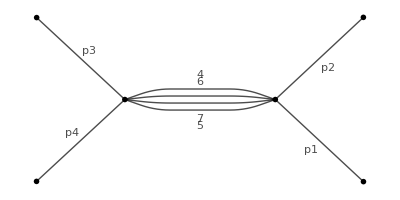
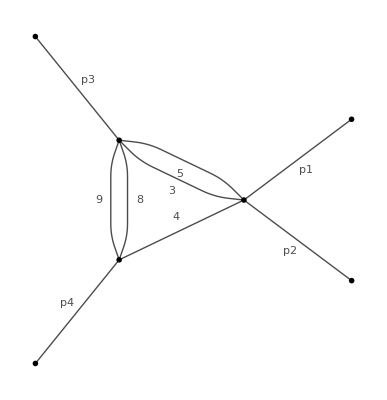
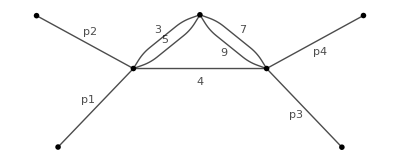
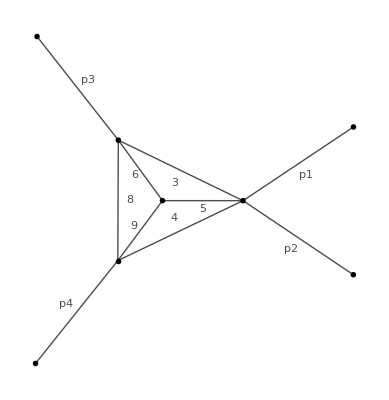
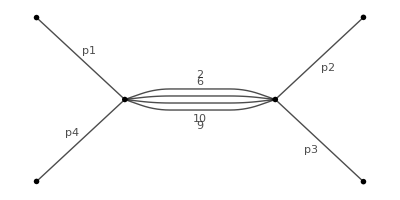
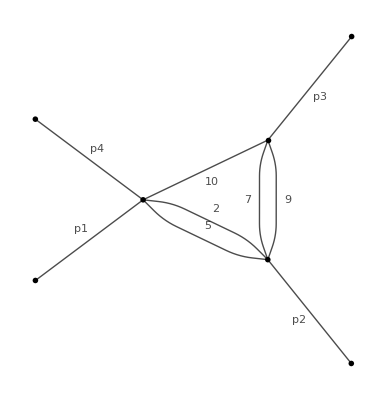
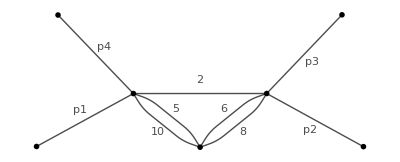
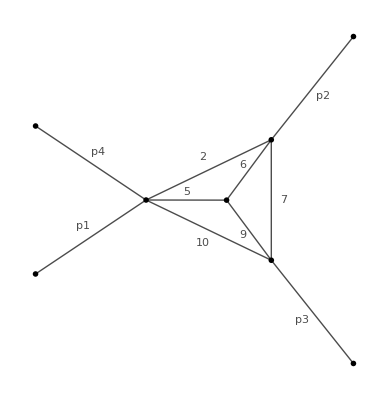

```mathematica
jGraphPlot/@masters
```

```mathematica
canonicalmasters=Import["FF/3LTC/can.m"]/.{_,{a__}}:>j[box3,a];
```

jGraph::nums: The numerator is not drawn!.

General::stop: Further output of jGraph::nums will be suppressed during this calculation.

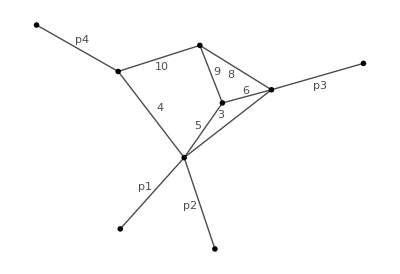
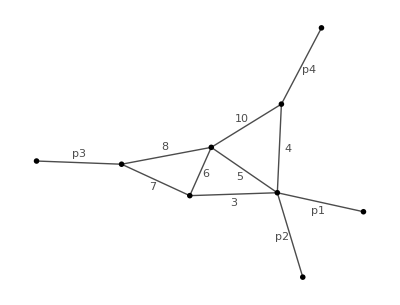
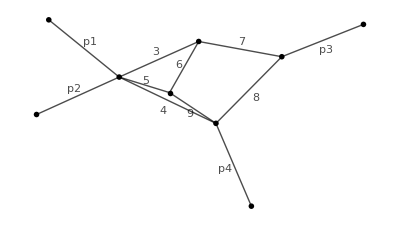
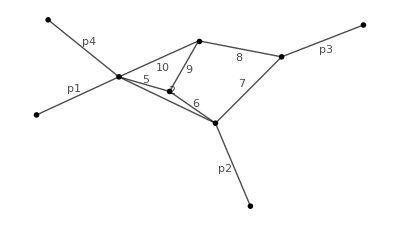
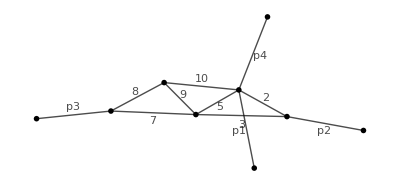
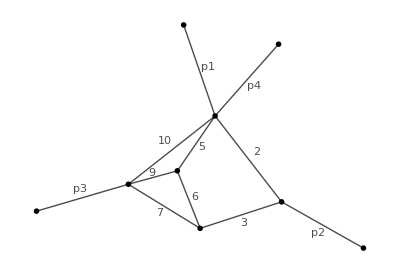
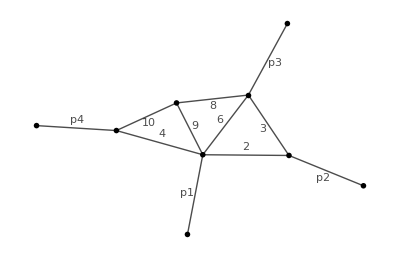
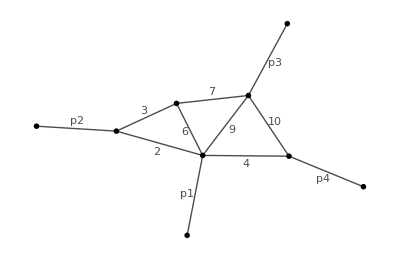
{s -Graphics-,s -Graphics-,s -Graphics-,t -Graphics-,(s+t) -Graphics-,s -Graphics-,t -Graphics-,t -Graphics-,(s+t) -Graphics-,(s+t) -Graphics-,t -Graphics-,s -Graphics-,s -Graphics-,s t -Graphics-,s t -Graphics-,s t -Graphics-,s t -Graphics-,s t -Graphics-,s^2 -Graphics-,s^2 -Graphics-,s t -Graphics-,s t -Graphics-,s^2 -Graphics-,s (s+t) -Graphics-,t -Graphics-+s t -Graphics-,s -Graphics-+s t -Graphics-,s -Graphics--t -Graphics-+t -Graphics--t -Graphics-,t -Graphics-,-2 s -Graphics--s -Graphics-+s -Graphics-+s -Graphics-,t -Graphics-+s -Graphics-,s -Graphics-,t -Graphics-+s -Graphics-+s t -Graphics-,s^2 t -Graphics-,s t -Graphics-,s^2 -Graphics-,s t -Graphics-,s^2 -Graphics-,-s^2 -Graphics--2 s^2 -Graphics-+2 s^2 -Graphics-,s^2 t -Graphics-,s^2 -Graphics-,-s t -Graphics-+s t -Graphics-+s t -Graphics-}

```mathematica
canonicalmasters/.Thread[Cases[canonicalmasters,_G,Infinity]->jGraphPlot/@(Cases[canonicalmasters,_G,Infinity]/.G[_,{a__}]:>j[box3,a])]
```

```mathematica
%20[[19]]
```

Part::partw: Part 19 of %20 does not exist.

%20⟦19⟧

## Differential equations matrix

```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../../"];
```

```mathematica
<<LiteRed2`
```

**************** LiteRed v2.025β ********************
Author: Roman N. Lee, Budker Institute of Nuclear Physics, Novosibirsk.
Release Date: ????-??-??
Timestamp: Thu 20 Nov 2025 13:50:10
Read from:/Users/corradini/LiteRed2/Source/LiteRed2025.m (CRC32:749265139,{2340977437, 3317197336, 1063727846})

LiteRed stands for Loop integrals Reduction.
The package is designed for the search and application of the Integration-By-Part reduction rules. It also contains some other useful tools.

See ?LiteRed`* for a list of functions.

```mathematica
Declare[{k1,k2,k3,p1,p2,p3},Vector,{s,t},Number];
sp[p1,p1]=0;sp[p2,p2]=0;sp[p3,p3]=0;sp[p1,p2]=s/2;sp[p2,p3]=t/2;sp[p1,p3]=(-s-t)/2;
```

```mathematica
NewDsBasis[box3,{-(k1·k1),-((k1+p1)·(k1+p1)),-((k1+p1+p2)·(k1+p1+p2)),-(k2·k2),-((-k1+k2)·(-k1+k2)),-((-k1+k2+k3)·(-k1+k2+k3)),-((k2+k3+p1+p2)·(k2+k3+p1+p2)),-((k2+k3+p1+p2+p3)·(k2+k3+p1+p2+p3)),-(k3·k3),-((k2+p1+p2+p3)·(k2+p1+p2+p3)),-((k2+p1)·(k2+p1)),-((k3+p1)·(k3+p1)),-((k1+p1+p2+p3)·(k1+p1+p2+p3)),-((k1+k3)·(k1+k3)),-((k2+p1+p2)·(k2+p1+p2))},{k1,k2,k3},Directory->"box3dir"];
```

box3 is valid basis. The definitions of the basis will be saved in "box3dir" directory.
    Ds[box3] — denominators,
    SPs[box3] — scalar products involving loop momenta,
    LMs[box3] — loop momenta,
    EMs[box3] — external momenta,
    Parameters[box3] — parameters (invariants, masses, dimension),
    Toj[box3] — rules to transform scalar products to denominators,
    CutDs[box3] — flag vector of cut denominators.

```mathematica
GenerateIBP[box3]
AnalyzeSectors[box3,{__,0,0,0,0,0}]
FindSymmetries[box3]
```

Identities are generated.
    IBP[box3] — integration-by-part identities,
    LI[box3] — Lorentz invariance identities.

Updated SectorsPattern[box3] — pattern for all relevant sectors of the basis box3.

Found 720(304) zero(nonzero) sectors out of 1024.
    ZeroSectors[box3] — zero sectors,
    NonZeroSectors[box3] — nonzero sectors,
    SimpleSectors[box3] — simple sectors (no nonzero subsectors),
    BasisSectors[box3] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[box3] — a rule to nullify all zero j[box3…],
    CutDs[box3] — a flag list of cut denominators (1=cut).

Found 172 mapped sectors and 132 unique sectors.
    UniqueSectors[box3] — unique sectors.
    MappedSectors[box3] — mapped sectors.
    SR[box3][…] — symmetry relations for j[box3,…] from UniqueSectors[box3].
    jSymmetries[box3,…] — symmetry rules for the sector js[box3,…] in UniqueSectors[box3].
    jRules[box3,…] — reduction rules for j[box3,…] from MappedSectors[box3].
    SectorsMappings[box3] gives the list of mappings of all sectors from MappedSectors[box3] to UniqueSectors[box3].

172

```mathematica
SectorOf[family_,exponents___]:=js[family,##]&@@(If[#>0,1,0]&/@{exponents});
SectorOf[j[family_,exponents___]]:=SectorOf[family,exponents];
```

```mathematica
ZeroQ[j[family_,a__]]:=MemberQ[ZeroSectors[family],SectorOf[j[family,a]]];
```

```mathematica
RemoveZeroSectors[expr_]:=expr /. Dispatch[(#->0)&/@Select[Cases[{expr},_j,Infinity]//DeleteDuplicates,ZeroQ]];
```

```mathematica
can=Import["FF/3LTC/BasisCh.m"]/.G[_,{a__}]:>j[box3,a];
```

```mathematica
ders=Dinv[#,s]&/@can//RemoveZeroSectors;
dert=Dinv[#,t]&/@can//RemoveZeroSectors;
```

```mathematica
Export["FF/3LTC/ders.m",ders];
Export["FF/3LTC/dert.m",dert];
```

```mathematica
jsder=Cases[Join[ders,dert],_j,Infinity]//DeleteDuplicates;
```

```mathematica
Export["FF/3LTC/wishlist_der.m",jsder/.{j[box3,a__]:>{1,{a}}}];
```

```mathematica
"FF/3LTC/wishlist_der.m"
```

```mathematica
Quit
```

### Run IBP reduction with 3LTCDer.config

## Build DE matrix

```mathematica
Quit
```

```mathematica
mastersLaporta=Import["FF/3LTC/mastersLadCan.m"];
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../../"];
Get["FIRE6.m"];
LoadStart["FF/3LTC/3LTC",1];
Burn[];
LoadTables["FF/3LTC/3LTCDer.tables"];
```

FIRE, version 6.5.2

Initial data loaded

```mathematica
masters=MasterIntegrals[];
```

```mathematica
SameQ[mastersLaporta,masters]
```

True

```mathematica
ders=(Import["FF/3LTC/ders.m"]/.j[_,a__]:>F[1,{a}]);
dert=(Import["FF/3LTC/dert.m"]/.j[_,a__]:>F[1,{a}]);
ders//Length
```

41

```mathematica
ds0=Table[Coefficient[ders[[i]],(masters[[k]]/.{{1,{a__}}:>G[1,{a}]})],{i,Length[ders]},{k,Length[masters]}];
dt0=Table[Coefficient[dert[[i]],(masters[[k]]/.{{1,{a__}}:>G[1,{a}]})],{i,Length[ders]},{k,Length[masters]}];
```

```mathematica
MIstoCanMatrix=Import["FF/3LTC/MIstoCan.m"];
```

```mathematica
ds=((ds0.MIstoCanMatrix)/.{d->4-2 eps})//Simplify;
dt=((dt0.MIstoCanMatrix)/.{d->4-2 eps})//Simplify;
```

$Aborted

```mathematica
Export["FF/3LTC/ds.m",ds];
Export["FF/3LTC/dt.m",dt];
```

## A first check: scaling and integrability conditions

```mathematica
ds=Import["FF/3LTC/ds.m"];
dt=Import["FF/3LTC/dt.m"];
```

```mathematica
s ds+t dt//Simplify//MatrixForm
```

(-3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps)

```mathematica
ds.dt-dt.ds-D[ds,t]+D[dt,s]//Simplify//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## Integrating the equations

## Computing matrix logarithmic form in x=t/s

```mathematica
alphaco={s,t,s+t}
```

{s,t,s+t}

```mathematica
cs=c/@Range[Length[alphaco]];
```

```mathematica
eqss=Table[Table[eqs[ii,jj],{jj,1,Length[ds]}],{ii,1,Length[ds]}];
eqts=Table[Table[eqt[ii,jj],{jj,1,Length[dt]}],{ii,1,Length[dt]}];
```

```mathematica
Do[eqs[ii,jj]=ds[[ii]][[jj]]==D[cs.(Log[#]&/@alphaco),s],{ii,1,Length[ds]},{jj,1,Length[ds]}];
Do[eqt[ii,jj]=dt[[ii]][[jj]]==D[cs.(Log[#]&/@alphaco),t],{ii,1,Length[dt]},{jj,1,Length[dt]}];
```

```mathematica
num50=Table[{s->RandomReal[WorkingPrecision->50],t->RandomReal[WorkingPrecision->50]},{i,1,50}];
```

```mathematica
Do[Do[Asol[ii,jj]=NSolve[Flatten[Table[{eqs[ii,jj],eqt[ii,jj]}/.num50[[iter]],{iter,1,20}]],cs]//Chop//Rationalize;If[Mod[ii,50]==0&&Mod[jj,50]==0,PrintTemporary["Done :: {",ii,",",jj,"}"]];,{ii,1,Length[ds]}],{jj,1,Length[ds]}]
```

```mathematica
Atilde=Table[Table[(cs.(Log[#]&/@alphaco))/.Flatten[Asol[ii,jj]],{jj,1,Length[ds]}],{ii,1,Length[ds]}]/._c->0;
Atildex=Collect[Atilde/.t->x s/.s->-1/.Log[a___]:>PowerExpand[Log[Factor[a]]]/.Log[-1-x]:>Log[1+x]/.Pi->0,Log[___],Together];
```

```mathematica
Export["FF/3LTC/Atilde.m",Atildex]
```

FF/3LTC/Atilde.m

```mathematica
Quit[]
```

## Integrating the differential equations

```mathematica
<<PolyLogTools`;
```

(****** PolyLogTools 1.4 ******)

Authors: Claude Duhr, Falko Dulat

Email: cduhr@uni-bonn.de

PolyLogTools uses the implementation of the PSLQ algorithm by P. Bertok (http://library.wolfram.com/infocenter/MathSource/4263/)

*-*-*-*-*-* HPL 2.0 *-*-*-*-*-*

Author: Daniel Maitre, University of Zurich

Rules for minimal set loaded for weights: 2, 3, 4, 5, 6.

Rules for minimal set for + - weights loaded for weights: 2, 3, 4, 5, 6.

Table of MZVs loaded up to weight 6

Table of values at I loaded up to weight 6

$HPLFunctions gives a list of the functions of the package.
$HPLOptions gives a list of the options of the package.

More info in hep-ph/0507152, hep-ph/0703052 and at 
 http://krone.physik.unizh.ch/~maitreda/HPL/

GraphJoin::shdw: Symbol GraphJoin appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

GraphProduct::shdw: Symbol GraphProduct appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

GraphSum::shdw: Symbol GraphSum appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

SetDelayed::write: Tag EdgeChromaticNumber in EdgeChromaticNumber[g_Graph] is Protected.

SetDelayed::write: Tag TreeQ in TreeQ[g_Graph] is Protected.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/corradini/fire/FIRE6/FF/3LTC

```mathematica
Atildex=Import["Atilde.m"];
```

```mathematica
Atildex//Variables
```

{eps,Log[x],Log[1+x]}

```mathematica
alphaco=Log[#]&/@{x,1+x};
```

### Weight 0

```mathematica
bdry0[0]=Table[b[i,0],{i,1,41}];
```

```mathematica
Table[A[i]=Coefficient[ Atildex,alphaco[[i]]],{i,1,2}];
```

```mathematica
Table[matexp[i]=MatrixExp[ Log[a] A[i]],{i,2}];
```

```mathematica
matexp[1]//Eigenvalues//DeleteDuplicates
```

{a^(-4 eps),a^(-3 eps),a^(-2 eps),1,a^eps,a^(3 eps)}

```mathematica
matexp[2]//Eigenvalues//DeleteDuplicates
```

{1,a^eps,a^(2 eps),a^(3 eps),a^(5 eps)}

```mathematica
eqs[1][0]=Thread[(Coefficient[matexp[1],a^(3eps)].(bdry0[0]))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[2][0]=Thread[(Coefficient[matexp[1],a^eps].(bdry0[0]))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[3][0]=Thread[(Coefficient[matexp[2],a^(5eps)].(bdry0[0]))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[4][0]=Thread[(Coefficient[matexp[2],a^(3eps)].(bdry0[0]))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[5][0]=Thread[(Coefficient[matexp[2],a^(2eps)].(bdry0[0]))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[6][0]=Thread[(Coefficient[matexp[2],a^eps].(bdry0[0]))==0]//DeleteCases[#,True]&;
```

```mathematica
sols[1][0]=Solve[Join[Join[eqs[1][0],eqs[2][0],eqs[3][0],eqs[4][0],eqs[5][0],eqs[6][0]]],bdry0[0]][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
bdryt[0]=bdry0[0]/.sols[1][0];
```

#### Weight 1

```mathematica
bdry0[1]=eps Table[b[i,1],{i,1,Length[bdry0[0]]}];
```

```mathematica
Mbt[1][0]=Map[GIntegrate[#,x]&,D[Simplify[Atildex.bdryt[0]],x]];
```

```mathematica
M0[1]=Mbt[1][0]+bdry0[1];
```

#### Fix remaining weight 0 constants

```mathematica
eqs[7][0]=Thread[(Im[Coefficient[matexp[2],a^eps].M0[1]/.x->-1]//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
eqs[8][0]=Thread[(Im[Coefficient[matexp[2],a^(2eps)].M0[1]/.x->-1]//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
eqs[9][0]=Thread[(Im[Coefficient[matexp[2],a^(3eps)].M0[1]/.x->-1]//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
eqs[10][0]=Thread[(Im[Coefficient[matexp[2],a^(5eps)].M0[1]/.x->-1]//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
```

```mathematica
finalBC=(BubbleB52.bdry0[0])
```

BubbleB52.{b[1,0],b[2,0],b[3,0],b[4,0],b[5,0],b[6,0],b[7,0],b[8,0],b[9,0],b[10,0],b[11,0],b[12,0],b[13,0],b[14,0],b[15,0],b[16,0],b[17,0],b[18,0],b[19,0],b[20,0],b[21,0],b[22,0],b[23,0],b[24,0],b[25,0],b[26,0],b[27,0],b[28,0],b[29,0],b[30,0],b[31,0],b[32,0],b[33,0],b[34,0],b[35,0],b[36,0],b[37,0],b[38,0],b[39,0],b[40,0],b[41,0]}

```mathematica
sols[2][0]=Solve[Join[eqs[7][0],eqs[8][0],eqs[9][0],eqs[10][0]]/.{Arg[a]->0},bdry0[0]][[1]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{b[1,0]→0,b[2,0]→0,b[3,0]→0,b[4,0]→0,b[8,0]→0,b[18,0]→3/2 b[19,0],b[20,0]→0,b[21,0]→0,b[23,0]→9/2 b[19,0],b[26,0]→0,b[28,0]→-1/2 b[19,0],b[29,0]→-3 b[19,0],b[36,0]→2 b[19,0],b[39,0]→-32 b[19,0]}

```mathematica
bdryf[0]=bdryt[0]/.sols[2][0]/.{b[19,0]->1/18}
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,1/12,0,0,1/12,1/18,0,0,0,1/4,0,0,0,0,-1/36,-1/6,0,0,0,-35/36,7/36,1/36,1/9,1/2,11/36,-16/9,7/9,10/9}

```mathematica
Mf[0]=bdryf[0]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,1/12,0,0,1/12,1/18,0,0,0,1/4,0,0,0,0,-1/36,-1/6,0,0,0,-35/36,7/36,1/36,1/9,1/2,11/36,-16/9,7/9,10/9}

#### Fix weight 1 constants

```mathematica
Mbf[1][0]=Map[GIntegrate[#,x]&,D[Simplify[Atildex.bdryf[0]],x]];
```

```mathematica
Mt[1]=Mbf[1][0]+bdry0[1]
```

{eps b[1,1],eps b[2,1],eps b[3,1],eps b[4,1],eps b[5,1],eps b[6,1],eps b[7,1],eps b[8,1],eps b[9,1],eps b[10,1],eps b[11,1],eps b[12,1],eps b[13,1],eps b[14,1]-1/2 eps G[0,x],eps b[15,1]-1/4 eps G[0,x],eps b[16,1],eps b[17,1],eps b[18,1],eps b[19,1],eps b[20,1],eps b[21,1],eps b[22,1],eps b[23,1],eps b[24,1],eps b[25,1],eps b[26,1],eps b[27,1],eps b[28,1]+1/12 eps G[0,x],eps b[29,1]+1/4 eps G[0,x],eps b[30,1],eps b[31,1],eps b[32,1],eps b[33,1]+eps G[0,x],eps b[34,1]-7/12 eps G[0,x],eps b[35,1],eps b[36,1]-1/3 eps G[0,x],eps b[37,1]-1/4 eps G[0,x],eps b[38,1]-1/2 eps G[0,x],eps b[39,1]+19/6 eps G[0,x],eps b[40,1]-eps G[0,x],eps b[41,1]-37/12 eps G[0,x]}

```mathematica
eqs[1][1]=Thread[(Coefficient[matexp[1],a^(3eps)].(Mt[1]/.x->0))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[2][1]=Thread[(Coefficient[matexp[1],a^eps].(Mt[1]/.x->0))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[3][1]=Thread[(Coefficient[matexp[2],a^(3eps)].(Mt[1]/.x->-1))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[4][1]=Thread[(Coefficient[matexp[2],a^(2eps)].(Mt[1]/.x->-1))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[5][1]=Thread[(Coefficient[matexp[2],a^eps].(Mt[1]/.x->-1))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[6][1]=Thread[(Coefficient[matexp[2],a^(5 eps)].(Mt[1]/.x->-1))==0]//DeleteCases[#,True]&;
```

```mathematica
sols[1][1]=Solve[Join[Join[eqs[1][1],eqs[2][1],eqs[3][1],eqs[4][1],eqs[5][1],eqs[6][1]]],bdry0[1]/eps][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
bdryt[1]=bdry0[1]/.sols[1][1];
```

### Weight 2

```mathematica
bdry0[2]=eps^2 Table[b[i,2],{i,1,Length[bdry0[0]]}];
Mbf[2][0]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[1][0])];
Mbt[1][1]=Map[GIntegrate[#,x]&,D[Atildex,x].bdryt[1]];
```

```mathematica
M0[2]=Mbf[2][0]+Mbt[1][1]+bdry0[2];
```

#### Fix remaining weight 1 constants

```mathematica
eqs[7][1]=Thread[(Im[Coefficient[matexp[2],a^eps].M0[2]/.x->-1]//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
eqs[8][1]=Thread[(Im[Coefficient[matexp[2],a^(2eps)].M0[2]/.x->-1]//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
eqs[9][1]=Thread[(Im[Coefficient[matexp[2],a^(3eps)].M0[2]/.x->-1]//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
eqs[10][1]=Thread[(Im[Coefficient[matexp[2],a^(5eps)].M0[2]/.x->-1]//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
```

```mathematica
sols[2][1]=Solve[Join[eqs[7][1],eqs[8][1],eqs[9][1],eqs[10][1]]/.{Arg[a]->0},bdry0[1]/eps][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
bdryf[1]=bdryt[1]/.sols[2][1]/.{b[19,1]->0};
```

```mathematica
Mf[1]=Mbf[1][0]+bdryf[1];
```

#### Fix weight 2 constants

```mathematica
Mbf[1][1]=Map[GIntegrate[#,x]&,D[Atildex,x].bdryf[1]];
```

```mathematica
Mt[2]=Mbf[2][0]+Mbf[1][1]+bdry0[2];
```

```mathematica
eqs[1][2]=Thread[(Coefficient[matexp[1],a^(3eps)].(Mt[2]/.x->0))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[2][2]=Thread[(Coefficient[matexp[1],a^eps].(Mt[2]/.x->0))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[3][2]=Thread[(Coefficient[matexp[2],a^(3eps)].(Mt[2]/.x->-1))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[4][2]=Thread[(Coefficient[matexp[2],a^(2eps)].(Mt[2]/.x->-1))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[5][2]=Thread[(Coefficient[matexp[2],a^eps].(Mt[2]/.x->-1))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[6][2]=Thread[(Coefficient[matexp[2],a^(5eps)].(Mt[2]/.x->-1))==0]//DeleteCases[#,True]&;
```

```mathematica
sols[1][2]=Solve[Join[Join[eqs[1][2],eqs[2][2],eqs[3][2],eqs[4][2],eqs[5][2],eqs[6][2]]],bdry0[2]/eps^2][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
bdryt[2]=bdry0[2]/.sols[1][2];
```

### Weight 3

```mathematica
bdry0[3]=eps^3 Table[b[i,3],{i,1,Length[bdry0[0]]}];
Mbf[3][0]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[2][0])];
Mbf[2][1]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[1][1])];
Mbt[1][2]=Map[GIntegrate[#,x]&,D[Atildex,x].bdryt[2]];
```

```mathematica
M0[3]=Mbf[3][0]+Mbf[2][1]+Mbt[1][2]+bdry0[3];
```

#### Fix remaining weight 2 constants

```mathematica
eqs[7][2]=Thread[(Im[Coefficient[matexp[2],a^eps].M0[3]/.x->-1]//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
eqs[8][2]=Thread[(Im[Coefficient[matexp[2],a^(2eps)].M0[3]/.x->-1]//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
eqs[9][2]=Thread[(Im[Coefficient[matexp[2],a^(3eps)].M0[3]/.x->-1]//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
eqs[10][2]=Thread[(Im[Coefficient[matexp[2],a^(4eps)].M0[3]/.x->-1]//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
```

```mathematica
sols[2][2]=Solve[Join[eqs[7][2],eqs[8][2],eqs[9][2],eqs[10][2]]/.{Arg[a]->0},bdry0[2]/eps^2][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
bdryf[2]=bdryt[2]/.sols[2][2]/.{b[19,2]->π^2/12};
```

```mathematica
Mf[2]=Mbf[2][0]+Mbf[1][1]+bdryf[2];
```

#### Fix weight 3 constants

```mathematica
Mbf[1][2]=Map[GIntegrate[#,x]&,D[Atildex,x].bdryf[2]];
```

```mathematica
Mt[3]=Mbf[3][0]+Mbf[2][1]+Mbf[1][2]+bdry0[3];
```

```mathematica
eqs[1][3]=Thread[(Coefficient[matexp[1],a^(3eps)].(Mt[3]/.x->0))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[2][3]=Thread[(Coefficient[matexp[1],a^eps].(Mt[3]/.x->0))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[3][3]=Thread[(Coefficient[matexp[2],a^(3eps)].(Mt[3]/.x->-1))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[4][3]=Thread[(Coefficient[matexp[2],a^(2eps)].(Mt[3]/.x->-1))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[5][3]=Thread[(Coefficient[matexp[2],a^eps].(Mt[3]/.x->-1))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[6][3]=Thread[(Coefficient[matexp[2],a^(5eps)].(Mt[3]/.x->-1))==0]//DeleteCases[#,True]&;
```

```mathematica
sols[1][3]=Solve[Join[Join[eqs[1][3],eqs[2][3],eqs[3][3],eqs[4][3],eqs[5][3],eqs[6][3]]],bdry0[3]/eps^3][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
bdryt[3]=bdry0[3]/.sols[1][3];
```

### Weight 4

```mathematica
bdry0[4]=eps^4 Table[b[i,4],{i,1,Length[bdry0[0]]}];
Mbf[4][0]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[3][0])];
Mbf[3][1]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[2][1])];
Mbf[2][2]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[1][2])];
Mbt[1][3]=Map[GIntegrate[#,x]&,D[Atildex,x].bdryt[3]];
```

```mathematica
M0[4]=Mbf[4][0]+Mbf[3][1]+Mbf[2][2]+Mbt[1][3]+bdry0[4];
```

#### Fix remaining weight 3 constants

```mathematica
Gs[4]=Cases[M0[4],_G,Infinity]//DeleteDuplicates
```

{G[0,x],G[-1,-1,x],G[-1,0,x],G[0,-1,x],G[0,0,x],G[-1,-1,0,0,x],G[-1,0,0,0,x],G[0,-1,0,0,x],G[0,0,0,0,x],G[-1,x]}

```mathematica
fb[4]=ReduceCG[Gs[4]/.x->-(1-δ),{δ,x},Point->{δ->3/13+ I Log[2] *10^(-30) , x.10-> 5/23+ I Log[2] *10^(-30)}];
```

```mathematica
eqs[7][3]=Thread[(Im[Coefficient[matexp[2],a^eps].M0[4]]/.x->δ-1/.fb[4]/.δ->0//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
eqs[8][3]=Thread[(Im[Coefficient[matexp[2],a^(2eps)].M0[4]]/.x->δ-1/.fb[4]/.δ->0//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
eqs[9][3]=Thread[(Im[Coefficient[matexp[2],a^(3eps)].M0[4]]/.x->δ-1/.fb[4]/.δ->0//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
eqs[10][3]=Thread[(Im[Coefficient[matexp[2],a^(5eps)].M0[4]]/.x->δ-1/.fb[4]/.δ->0//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
```

```mathematica
sols[2][3]=Solve[Join[eqs[7][3],eqs[8][3],eqs[9][3],eqs[10][3]]/.{Arg[a]->0},bdry0[3]/eps^3][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
bdryf[3]=bdryt[3]/.sols[2][3]/.{b[19,3]->(35 Zeta[3])/18};
```

```mathematica
Mf[3]=Mbf[3][0]+Mbf[2][1]+Mbf[1][2]+bdryf[3];
```

#### Fix weight 4 constants

```mathematica
Mbf[1][3]=Map[GIntegrate[#,x]&,D[Atildex,x].bdryf[3]];
```

```mathematica
Mt[4]=Mbf[4][0]+Mbf[3][1]+Mbf[2][2]+Mbf[1][3]+bdry0[4];
```

```mathematica
eqs[1][4]=Thread[(Coefficient[matexp[1],a^(3eps)].(Mt[4]/.x->δ-1/.fb[4]/.δ->1))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[2][4]=Thread[(Coefficient[matexp[1],a^eps].(Mt[4]/.x->δ-1/.fb[4]/.δ->1))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[3][4]=Thread[(Coefficient[matexp[2],a^(3eps)].(Mt[4]/.x->δ-1/.fb[4]/.δ->0))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[4][4]=Thread[(Coefficient[matexp[2],a^(2eps)].(Mt[4]/.x->δ-1/.fb[4]/.δ->0))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[5][4]=Thread[(Coefficient[matexp[2],a^eps].(Mt[4]/.x->δ-1/.fb[4]/.δ->0))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[6][4]=Thread[(Coefficient[matexp[2],a^(5eps)].(Mt[4]/.x->δ-1/.fb[4]/.δ->0))==0]//DeleteCases[#,True]&;
```

```mathematica
sols[1][4]=Solve[Join[Join[eqs[1][4],eqs[2][4],eqs[3][4],eqs[4][4],eqs[5][4],eqs[6][4]]],bdry0[4]/eps^4][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
bdryt[4]=bdry0[4]/.sols[1][4];
```

### Weight 5

```mathematica
bdry0[5]=eps^5 Table[b[i,5],{i,1,Length[bdry0[0]]}];
Mbf[5][0]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[4][0])];
Mbf[4][1]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[3][1])];
Mbf[3][2]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[2][2])];
Mbf[2][3]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[1][3])];
Mbt[1][4]=Map[GIntegrate[#,x]&,D[Atildex,x].bdryt[4]];
```

```mathematica
M0[5]=Mbf[5][0]+Mbf[4][1]+Mbf[3][2]+Mbf[2][3]+Mbt[1][4]+bdry0[5];
```

#### Fix remaining weight 4 constants

```mathematica
Gs[5]=Cases[M0[5],_G,Infinity]//DeleteDuplicates
```

{G[0,x],G[0,0,x],G[0,-1,0,x],G[0,0,-1,x],G[0,0,0,x],G[0,-1,0,0,0,x],G[0,0,-1,0,0,x],G[-1,x],G[-1,-1,-1,x],G[-1,-1,0,x],G[-1,0,-1,x],G[-1,0,0,x],G[0,-1,-1,x],G[-1,-1,-1,0,0,x],G[-1,-1,0,0,0,x],G[-1,0,-1,0,0,x],G[-1,0,0,0,0,x],G[0,-1,-1,0,0,x],G[0,0,0,0,0,x],G[-1,-1,x],G[-1,0,x],G[0,-1,x]}

```mathematica
fb[5]=ReduceCG[Gs[5]/.x->-(1-δ),{δ,x},Point->{δ->3/13+ I Log[2] *10^(-30) , x.10-> 5/23+ I Log[2] *10^(-30)}];
```

```mathematica
eqs[7][4]=Thread[(Im[Coefficient[matexp[2],a^eps].M0[5]]/.x->δ-1/.fb[5]/.δ->0//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
eqs[8][4]=Thread[(Im[Coefficient[matexp[2],a^(2eps)].M0[5]]/.x->δ-1/.fb[5]/.δ->0//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
eqs[9][4]=Thread[(Im[Coefficient[matexp[2],a^(3eps)].M0[5]]/.x->δ-1/.fb[5]/.δ->0//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
eqs[10][4]=Thread[(Im[Coefficient[matexp[2],a^(5eps)].M0[5]]/.x->δ-1/.fb[5]/.δ->0//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
```

```mathematica
sols[2][4]=Solve[Join[eqs[7][4],eqs[8][4],eqs[9][4],eqs[10][4]]/.{Arg[a]->0},bdry0[4]/eps^4][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
bdryf[4]=bdryt[4]/.sols[2][4]/.{b[19,4]->(37 π^4)/540};
```

```mathematica
Mf[4]=Mbf[4][0]+Mbf[3][1]+Mbf[2][2]+Mbf[1][3]+bdryf[4];
```

#### Fix weight 5 constants

```mathematica
Mbf[1][4]=Map[GIntegrate[#,x]&,D[Atildex,x].bdryf[4]];
```

```mathematica
Mt[5]=Mbf[5][0]+Mbf[4][1]+Mbf[3][2]+Mbf[2][3]+Mbf[1][4]+bdry0[5];
```

```mathematica
eqs[1][5]=Thread[(Coefficient[matexp[1],a^(3eps)].(Mt[5]/.x->δ-1/.fb[5]/.δ->1))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[2][5]=Thread[(Coefficient[matexp[1],a^eps].(Mt[5]/.x->δ-1/.fb[5]/.δ->1))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[3][5]=Thread[(Coefficient[matexp[2],a^(3eps)].(Mt[5]/.x->δ-1/.fb[5]/.δ->0))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[4][5]=Thread[(Coefficient[matexp[2],a^(2eps)].(Mt[5]/.x->δ-1/.fb[5]/.δ->0))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[5][5]=Thread[(Coefficient[matexp[2],a^eps].(Mt[5]/.x->δ-1/.fb[5]/.δ->0))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[6][5]=Thread[(Coefficient[matexp[2],a^(5eps)].(Mt[5]/.x->δ-1/.fb[5]/.δ->0))==0]//DeleteCases[#,True]&;
```

```mathematica
sols[1][5]=Solve[Join[Join[eqs[1][5],eqs[2][5],eqs[3][5],eqs[4][5],eqs[5][5],eqs[6][5]]],bdry0[5]/eps^5][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
bdryt[5]=bdry0[5]/.sols[1][5];
```

### Weight 6

```mathematica
bdry0[6]=eps^6 Table[b[i,6],{i,1,Length[bdry0[0]]}];
Mbf[6][0]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[5][0])];
Mbf[5][1]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[4][1])];
Mbf[4][2]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[3][2])];
Mbf[3][3]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[2][3])];
Mbf[2][4]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[1][4])];
Mbt[1][5]=Map[GIntegrate[#,x]&,D[Atildex,x].bdryt[5]];
```

```mathematica
M0[6]=Mbf[6][0]+Mbf[5][1]+Mbf[4][2]+Mbf[3][3]+Mbf[2][4]+Mbt[1][5]+bdry0[6];
```

#### Fix remaining weight 5 constants. Define weight 6 GPL reductions in “fbweight6+.nb”

```mathematica
Cases[M0[6],_G,Infinity]//DeleteDuplicates
```

{G[0,x],G[0,0,x],G[0,0,0,x],G[-1,0,x],G[-1,0,-1,0,x],G[-1,0,0,-1,x],G[-1,0,0,0,x],G[0,-1,-1,0,x],G[0,-1,0,-1,x],G[0,-1,0,0,x],G[0,0,-1,-1,x],G[0,0,-1,0,x],G[0,0,0,-1,x],G[0,0,0,0,x],G[-1,0,-1,0,0,0,x],G[-1,0,0,-1,0,0,x],G[0,-1,-1,0,0,0,x],G[0,-1,0,-1,0,0,x],G[0,-1,0,0,0,0,x],G[0,0,-1,-1,0,0,x],G[0,0,-1,0,0,0,x],G[0,0,0,-1,0,0,x],G[-1,0,0,x],G[0,-1,0,x],G[0,0,-1,x],G[-1,x],G[-1,-1,x],G[0,-1,x],G[-1,-1,-1,-1,x],G[-1,-1,-1,0,x],G[-1,-1,0,-1,x],G[-1,-1,0,0,x],G[-1,0,-1,-1,x],G[0,-1,-1,-1,x],G[-1,-1,-1,-1,0,0,x],G[-1,-1,-1,0,0,0,x],G[-1,-1,0,-1,0,0,x],G[-1,-1,0,0,0,0,x],G[-1,0,-1,-1,0,0,x],G[-1,0,0,0,0,0,x],G[0,-1,-1,-1,0,0,x],G[0,0,0,0,0,0,x],G[-1,-1,-1,x],G[-1,-1,0,x],G[-1,0,-1,x],G[0,-1,-1,x]}

```mathematica
Gs[6]=Select[Cases[M0[6]/.RulesWeight6,_G,Infinity],TranscendentalWeight[#]<6&]//DeleteDuplicates
```

{G[0,x],G[0,0,x],G[0,0,0,x],G[-1,0,x],G[-1,0,-1,0,x],G[-1,0,0,-1,x],G[-1,0,0,0,x],G[0,-1,-1,0,x],G[0,-1,0,-1,x],G[0,-1,0,0,x],G[0,0,-1,-1,x],G[0,0,-1,0,x],G[0,0,0,-1,x],G[0,0,0,0,x],G[-1,0,0,x],G[0,-1,0,x],G[0,0,-1,x],G[-1,x],G[-1,-1,x],G[0,-1,x],G[-1,-1,-1,-1,x],G[-1,-1,-1,0,x],G[-1,-1,0,-1,x],G[-1,-1,0,0,x],G[-1,0,-1,-1,x],G[0,-1,-1,-1,x],G[-1,-1,-1,x],G[-1,-1,0,x],G[-1,0,-1,x],G[0,-1,-1,x]}

```mathematica
fb[6]=ReduceCG[Gs[6]/.x->-(1-δ),{δ,x},Point->{δ->7/13+ I Log[2] *10^(-30) , x.10-> 5/23+ I Log[2] *10^(-30)}];
```

```mathematica
eqs[7][5]=Thread[((Im[Coefficient[matexp[2],a^eps].M0[6]]/.x->δ-1/.RulesWeight6)
/.fb[6]/.δ->0//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
eqs[8][5]=Thread[((Im[Coefficient[matexp[2],a^(2eps)].M0[6]]/.x->δ-1/.RulesWeight6)
/.fb[6]/.δ->0//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
eqs[9][5]=Thread[((Im[Coefficient[matexp[2],a^(3eps)].M0[6]]/.x->δ-1/.RulesWeight6)
/.fb[6]/.δ->0//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
eqs[10][5]=Thread[((Im[Coefficient[matexp[2],a^(5eps)].M0[6]]/.x->δ-1/.RulesWeight6)
/.fb[6]/.δ->0//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
```

```mathematica
sols[2][5]=Solve[Join[eqs[7][5],eqs[8][5],eqs[9][5],eqs[10][5]]/.{Arg[a]->0},bdry0[5]/eps^5][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
bdryf[5]=bdryt[5]/.sols[2][5]/.{b[19,5]->(-10 π^2 Zeta[3]+147 Zeta[5])/6};
```

```mathematica
Mf[5]=Mbf[5][0]+Mbf[4][1]+Mbf[3][2]+Mbf[2][3]+Mbf[1][4]+bdryf[5]
```

#### Fix weight 6 constants

```mathematica
Mbf[1][5]=Map[GIntegrate[#,x]&,D[Atildex,x].bdryf[5]];
```

```mathematica
Mt[6]=Mbf[6][0]+Mbf[5][1]+Mbf[4][2]+Mbf[3][3]+Mbf[2][4]+Mbf[1][5]+bdry0[6];
```

```mathematica
eqs[1][6]=Thread[(Coefficient[matexp[1],a^(3eps)].(Mt[6]/.x->δ-1/.RulesWeight6/.fb[6]/.δ->1))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[2][6]=Thread[(Coefficient[matexp[1],a^eps].(Mt[6]/.x->δ-1/.RulesWeight6/.fb[6]/.δ->1))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[3][6]=Thread[(Coefficient[matexp[2],a^(3eps)].(Mt[6]/.x->δ-1/.RulesWeight6/.fb[6]/.δ->0))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[4][6]=Thread[(Coefficient[matexp[2],a^(2eps)].(Mt[6]/.x->δ-1/.RulesWeight6/.fb[6]/.δ->0))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[5][6]=Thread[(Coefficient[matexp[2],a^eps].(Mt[6]/.x->δ-1/.RulesWeight6/.fb[6]/.δ->0))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[6][6]=Thread[(Coefficient[matexp[2],a^(5eps)].(Mt[6]/.x->δ-1/.RulesWeight6/.fb[6]/.δ->0))==0]//DeleteCases[#,True]&;
```

```mathematica
sols[1][6]=Solve[Join[Join[eqs[1][6],eqs[2][6],eqs[3][6],eqs[4][6],eqs[5][6],eqs[6][6]]],bdry0[6]/eps^6][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
bdryt[6]=bdry0[6]/.sols[1][6];
```

### Weight 7

```mathematica
bdry0[7]=eps^7 Table[b[i,7],{i,1,Length[bdry0[0]]}];
Mbf[7][0]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[6][0])];
Mbf[6][1]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[5][1])];
Mbf[5][2]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[4][2])];
Mbf[4][3]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[3][3])];
Mbf[3][4]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[2][4])];
Mbf[2][5]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[1][5])];
Mbt[1][6]=Map[GIntegrate[#,x]&,D[Atildex,x].bdryt[6]];
```

```mathematica
M0[7]=Mbf[7][0]+Mbf[6][1]+Mbf[5][2]+Mbf[4][3]+Mbf[3][4]+Mbf[2][5]+Mbt[1][6]+bdry0[7]
```

#### Fix remaining weight 6 constants. Define weight 7 GPL reductions in “fbweight6+.nb”

```mathematica
Cases[M0[7],_G,Infinity]//DeleteDuplicates
```

{G[0,x],G[0,0,0,x],G[0,0,0,0,x],G[0,0,x],G[-1,-1,0,x],G[-1,0,0,x],G[0,-1,-1,x],G[0,-1,0,x],G[0,0,-1,x],G[-1,-1,0,-1,0,x],G[-1,-1,0,0,-1,x],G[-1,-1,0,0,0,x],G[-1,0,-1,-1,0,x],G[-1,0,-1,0,-1,x],G[-1,0,-1,0,0,x],G[-1,0,0,-1,-1,x],G[-1,0,0,-1,0,x],G[-1,0,0,0,-1,x],G[-1,0,0,0,0,x],G[0,-1,-1,-1,0,x],G[0,-1,-1,0,-1,x],G[0,-1,-1,0,0,x],G[0,-1,0,-1,-1,x],G[0,-1,0,-1,0,x],G[0,-1,0,0,-1,x],G[0,-1,0,0,0,x],G[0,0,-1,-1,-1,x],G[0,0,-1,-1,0,x],G[0,0,-1,0,0,x],G[0,0,0,-1,-1,x],G[0,0,0,-1,0,x],G[0,0,0,0,-1,x],G[0,0,0,0,0,x],G[-1,-1,0,-1,0,0,0,x],G[-1,-1,0,0,-1,0,0,x],G[-1,0,-1,-1,0,0,0,x],G[-1,0,-1,0,-1,0,0,x],G[-1,0,-1,0,0,0,0,x],G[-1,0,0,-1,-1,0,0,x],G[-1,0,0,-1,0,0,0,x],G[-1,0,0,0,-1,0,0,x],G[0,-1,-1,-1,0,0,0,x],G[0,-1,-1,0,-1,0,0,x],G[0,-1,-1,0,0,0,0,x],G[0,-1,0,-1,-1,0,0,x],G[0,-1,0,-1,0,0,0,x],G[0,-1,0,0,-1,0,0,x],G[0,-1,0,0,0,0,0,x],G[0,0,-1,-1,-1,0,0,x],G[0,0,-1,-1,0,0,0,x],G[0,0,-1,0,0,0,0,x],G[0,0,0,-1,-1,0,0,x],G[0,0,0,-1,0,0,0,x],G[0,0,0,0,-1,0,0,x],G[-1,-1,0,0,x],G[-1,0,-1,0,x],G[-1,0,0,-1,x],G[-1,0,0,0,x],G[0,-1,-1,0,x],G[0,-1,0,-1,x],G[0,-1,0,0,x],G[0,0,-1,-1,x],G[0,0,-1,0,x],G[0,0,0,-1,x],G[-1,x],G[-1,0,x],G[0,-1,x],G[-1,-1,x],G[-1,-1,-1,x],G[-1,0,-1,x],G[-1,-1,-1,-1,-1,x],G[-1,-1,-1,-1,0,x],G[-1,-1,-1,0,-1,x],G[-1,-1,-1,0,0,x],G[-1,-1,0,-1,-1,x],G[-1,0,-1,-1,-1,x],G[0,-1,-1,-1,-1,x],G[0,0,-1,0,-1,x],G[-1,-1,-1,-1,-1,0,0,x],G[-1,-1,-1,-1,0,0,0,x],G[-1,-1,-1,0,-1,0,0,x],G[-1,-1,-1,0,0,0,0,x],G[-1,-1,0,-1,-1,0,0,x],G[-1,-1,0,0,0,0,0,x],G[-1,0,-1,-1,-1,0,0,x],G[-1,0,0,0,0,0,0,x],G[0,-1,-1,-1,-1,0,0,x],G[0,0,-1,0,-1,0,0,x],G[0,0,0,0,0,0,0,x],G[-1,-1,-1,-1,x],G[-1,-1,-1,0,x],G[-1,-1,0,-1,x],G[-1,0,-1,-1,x],G[0,-1,-1,-1,x]}

```mathematica
Gs[7]=Select[Cases[M0[7]/.RulesWeight7,_G,Infinity],TranscendentalWeight[#]<7&]//DeleteDuplicates
```

{G[0,x],G[0,0,0,x],G[0,0,0,0,x],G[0,0,x],G[-1,-1,0,x],G[-1,0,0,x],G[0,-1,-1,x],G[0,-1,0,x],G[0,0,-1,x],G[-1,-1,0,-1,0,x],G[-1,-1,0,0,-1,x],G[-1,-1,0,0,0,x],G[-1,0,-1,-1,0,x],G[-1,0,-1,0,-1,x],G[-1,0,-1,0,0,x],G[-1,0,0,-1,-1,x],G[-1,0,0,-1,0,x],G[-1,0,0,0,-1,x],G[-1,0,0,0,0,x],G[0,-1,-1,-1,0,x],G[0,-1,-1,0,-1,x],G[0,-1,-1,0,0,x],G[0,-1,0,-1,-1,x],G[0,-1,0,-1,0,x],G[0,-1,0,0,-1,x],G[0,-1,0,0,0,x],G[0,0,-1,-1,-1,x],G[0,0,-1,-1,0,x],G[0,0,-1,0,0,x],G[0,0,0,-1,-1,x],G[0,0,0,-1,0,x],G[0,0,0,0,-1,x],G[0,0,0,0,0,x],G[-1,-1,0,0,x],G[-1,0,-1,0,x],G[-1,0,0,-1,x],G[-1,0,0,0,x],G[0,-1,-1,0,x],G[0,-1,0,-1,x],G[0,-1,0,0,x],G[0,0,-1,-1,x],G[0,0,-1,0,x],G[0,0,0,-1,x],G[-1,x],G[-1,0,x],G[0,-1,x],G[-1,-1,x],G[-1,-1,-1,x],G[-1,0,-1,x],G[-1,-1,-1,-1,-1,x],G[-1,-1,-1,-1,0,x],G[-1,-1,-1,0,-1,x],G[-1,-1,-1,0,0,x],G[-1,-1,0,-1,-1,x],G[-1,0,-1,-1,-1,x],G[0,-1,-1,-1,-1,x],G[0,0,-1,0,-1,x],G[-1,-1,-1,-1,x],G[-1,-1,-1,0,x],G[-1,-1,0,-1,x],G[-1,0,-1,-1,x],G[0,-1,-1,-1,x]}

```mathematica
fb[7]=ReduceCG[Gs[7]/.x->-(1-δ),{δ,x},Point->{δ->3/13+ I Log[2] *10^(-30) , x.10-> 5/23+ I Log[2] *10^(-30)}];
```

```mathematica
eqs[7][6]=Thread[(Im[(Coefficient[matexp[2],a^eps].M0[7]/.x->δ-1/.RulesWeight7)/.fb[7]/.δ->0]//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
eqs[8][6]=Thread[(Im[(Coefficient[matexp[2],a^(2 eps)].M0[7]/.x->δ-1/.RulesWeight7)/.fb[7]/.δ->0]//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
eqs[9][6]=Thread[(Im[(Coefficient[matexp[2],a^(3 eps)].M0[7]/.x->δ-1/.RulesWeight7)/.fb[7]/.δ->0]//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
eqs[10][6]=Thread[(Im[(Coefficient[matexp[2],a^(5 eps)].M0[7]/.x->δ-1/.RulesWeight7)/.fb[7]/.δ->0]//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
```

```mathematica
sols[2][6]=Solve[Join[eqs[7][6],eqs[8][6],eqs[9][6],eqs[10][6]]/.{Arg[a]->0},bdry0[6]/eps^6][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
bdryf[6]=bdryt[6]/.sols[2][6]/.{b[19,6]->(3121 π^6)/68040-(380 Zeta[3]^2)/9};
```

```mathematica
Mf[6]=Mbf[6][0]+Mbf[5][1]+Mbf[4][2]+Mbf[3][3]+Mbf[2][4]+Mbf[1][5]+bdryf[6];
```

### Solution

```mathematica
fullsol=Mf[0]+Mf[1]+Mf[2]+Mf[3]+Mf[4]+Mf[5]+Mf[6]
```

```mathematica
Export["fullsol.m",fullsol]
```

fullsol.m

```mathematica
Import["fullsol.m"]//Length
```

41

26

## Check

```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/corradini/fire/FIRE6/FF/3LTC

```mathematica
(Import["MIstoCan.m"].Import["fullsol.m"])[[1]]//FullSimplify
```

(eps^5 s^2 (-135+63 eps^4 π^4+3780 eps^3 Zeta[3]+40 eps^6 (2 π^6-1323 Zeta[3]^2)+34020 eps^5 Zeta[5]))/(810 (-6+71 eps-321 eps^2+694 eps^3-720 eps^4+288 eps^5))

```mathematica
(Import["MIstoCan.m"].Import["fullsol.m"])[[3]]//FullSimplify
```

-(eps^4 s (-1890+eps^3 (41580 Zeta[3]+eps (693 π^4+940 eps^2 π^6+3780 eps (-121 eps Zeta[3]^2+105 Zeta[5])))))/(5670 (-1+2 eps)^3 (-1+4 eps))

```mathematica
Normal @ Series[(Import["MIstoCan.m"].Import["fullsol.m"])[[6]]/(t eps^6),{eps,0,0}]
```

1/(6 eps^2)+(10-3 G[0,x])/(6 eps)+1/12 (128+π^2-60 G[0,x]+18 G[0,0,x])

```mathematica
1/(6 eps^2)(1-3 Log[x]+9(Log[x])^2)+5/(3 eps)(1-3 Log[x])+1/12 (128+π^2)
```

```mathematica
Normal@ Series[-A52/.{ε->eps},{eps,0,0}]
```

1/(6 eps^2)+5/(3 eps)+1/12 (128+π^2)